```mathematica
p=10;
s=0.05;
x0=0.5;
b=3;
c=1;
N0=4;
k=100;
```

```mathematica
original=NDSolve[{D[x[t],t]==-s*(1+p*x[t])*x[t]*(1-x[t]),x[0]==x0},x[t],{t,0,50}]
```

{{x[t]→InterpolatingFunction[{{0.,50.}},<>][t]}}

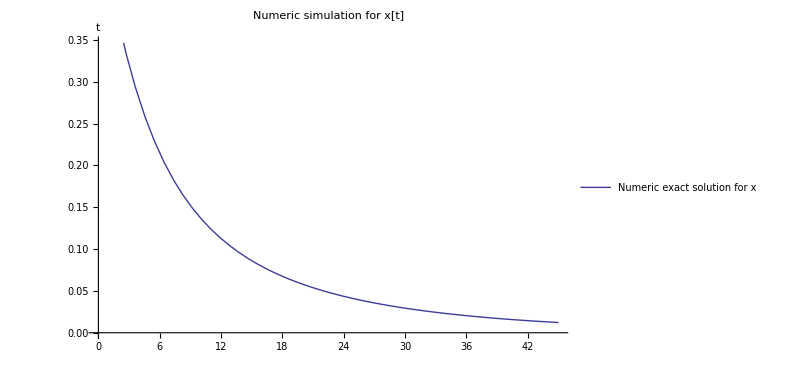

```mathematica
Plot[Evaluate[x[t]/.original],{t,0,45},PlotLegends->Placed[{"Numeric exact solution for x"},{0.65,0.8}],AxesLabel->{"t"},PlotLabel->"Numeric simulation for x[t]",ImageSize->600]
```